```mathematica
OS="linux";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata\\p-beam-current"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="linux",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/analysis-mirror_neutrons/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata/p-beam-current"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]];
metalvl3={Real,Real,Real,Real,Real,Real,Real,Real};
```

Working Directory: /home/prajwal/Dropbox/nEDM/analysis-mirror_neutrons/nstar_online

(AscDir) Rawdata Directory: /home/prajwal/Dropbox/nEDM/rawdata/p-beam-current

(ScrDir) Scratch Directory: /home/prajwal/Dropbox/Scratch

(PicDir) Picture Directory: /home/prajwal/Dropbox/nEDM/Pictures

(SysDir) System Directory: /home/prajwal/Dropbox/nEDM/system

Rawdata on mpc1636:/xdata/nedm_data/RawData

```mathematica
dat=ReadList[StringJoin[AscDir,seperator,"ucn_25sec_1190.txt"],Table[Real,{k,1,33}]]; (*2017*)
dat2=ReadList[StringJoin[AscDir,seperator,"ucn_25sec_5222.txt"],Table[Real,{k,1,33}]]; (*2016*)
dat3=ReadList[StringJoin[AscDir,seperator,"ucn_25sec_8367.txt"],Table[Real,{k,1,33}]]; (*12/2015*)
dat4=ReadList[StringJoin[AscDir,seperator,"ucn_25sec_8745.txt"],Table[Real,{k,1,33}]]; (*08/2015*)
(*dat5=ReadList[StringJoin[AscDir,seperator,"ucn_25sec_5695.txt"],Table[Real,{k,1,33}]]; (*10/2015*)*)
ptdat=Table[{dat[[k]][[1]],dat[[k]][[11]]/4},{k,1,Dimensions[dat][[1]]}];
ptdat2=Table[{dat2[[k]][[1]],dat2[[k]][[11]]/4},{k,1,Dimensions[dat2][[1]]}];
ptdat3=Table[{dat3[[k]][[1]],dat3[[k]][[11]]/4},{k,1,Dimensions[dat3][[1]]}];
ptdat4=Table[{dat4[[k]][[1]],dat4[[k]][[11]]/4},{k,1,Dimensions[dat4][[1]]}];
(*ptdat5=Table[{dat5[[k]][[1]],dat5[[k]][[11]]/4},{k,1,Dimensions[dat5][[1]]}];*)
```

```mathematica
exppt=ListPlot[{ptdat,ptdat2,ptdat3,ptdat4(*,ptdat5*)},Joined->True,Frame->True,FrameLabel->{"t_(After - Pilot - Kick)(s)","Proton Beam Current, I_(p^+)(mA)"},PlotLegends->{"2017","2016","12/2015","08/2015"(*,"10/2015"*)},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic,Medium}];
```

```mathematica
Export[StringJoin[PicDir,seperator,"p-current.png"],exppt]
```

C:\Users\tmpra\Dropbox\nEDM\Pictures\p-current.png

## Charge On Target, Charge on Target / Day

```mathematica
metaStructure3={Word,Real};
metaStructure4={Word,Real,Real};
(*6->HV, SF1->25, SF2->26,U->27,D->28,U+D->,Monitor->30,TotN->32,Fill->31,RF->-1*)
data=ReadList[StringJoin[AscDir,seperator,"p-pulseCount.txt"],metaStructure3];
data2=ReadList[StringJoin[AscDir,seperator,"combinedIntCur.txt"],metaStructure4];
ptdata=Table[{0,0},{k,1,Dimensions[data][[1]]}];
k=1;ini=0;fin=0;
sttime=AbsoluteTime[DateObject[data[[1]][[1]]]];
end=Dimensions[data][[1]];
For[i=2,i≤end,i++,
If[ToExpression[StringTake[data[[i]][[1]],{9,10}]]!=ToExpression[StringTake[data[[i-1]][[1]],{9,10}]],
ini=fin+1;
fin=i-1;
ptdata[[k]]={(AbsoluteTime[StringJoin[StringTake[data[[ini]][[1]],{1,10}],"_12:00:00_UTC"]]-sttime)/(24*3600),data[[fin]][[2]]-data[[ini]][[2]]};
If[Abs[ptdata[[k]][[2]]]>500,
ptdata[[k]][[2]]=0;
];
k++;
];
If[i==end,
ini=fin+1;
fin=end;
ptdata[[k]]={(AbsoluteTime[StringJoin[StringTake[data[[ini]][[1]],{1,10}],"_12:00:00_UTC"]]-sttime)/(24*3600),data[[fin]][[2]]-data[[ini]][[2]]};
If[Abs[ptdata[[k]][[2]]]>500,
ptdata[[k]][[2]]=0;
];
k++;
];
];
end2=Dimensions[data2][[1]];
ptdata2=Table[{0,0},{k,1,Dimensions[data2][[1]]}];
ptdata3=Table[{0,0},{k,1,Dimensions[data2][[1]]}];
sttime2=AbsoluteTime[DateObject[data2[[1]][[1]]]];
stcur=data2[[1]][[2]];l=1;
For[i=1,i≤end2,i++,
ptdata2[[i]]={(AbsoluteTime[data2[[i]][[1]]]-sttime2)/(24*3600),(data2[[i]][[3]]-data2[[i]][[2]])/1000};
If[MemberQ[{14,55,214,259,295,378,449,678},ptdata2[[i]][[1]]],
stcur=data2[[i]][[2]];
];
ptdata3[[i]]={(AbsoluteTime[data2[[i]][[1]]]-sttime2)/(24*3600),(data2[[i]][[3]]-stcur)/1000};
];
(*****************)
```

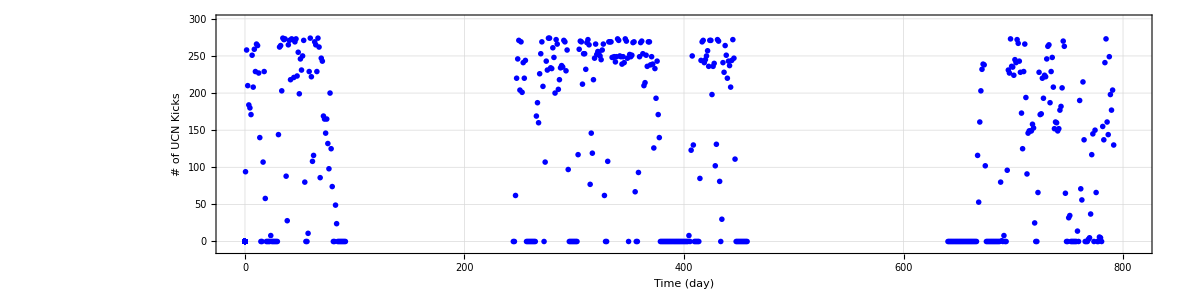

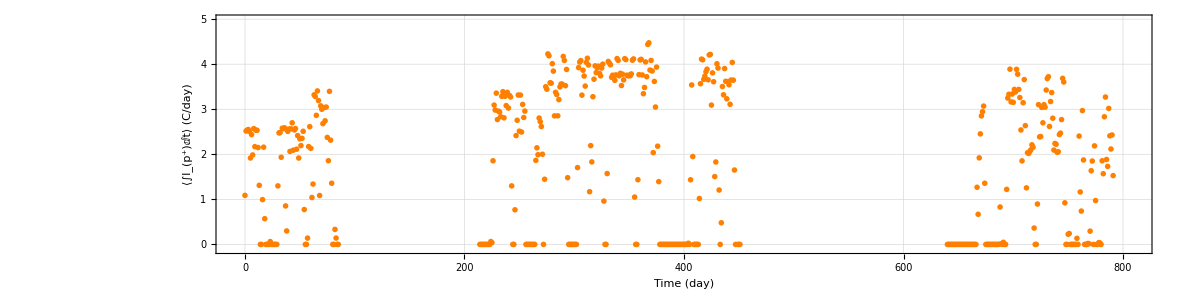

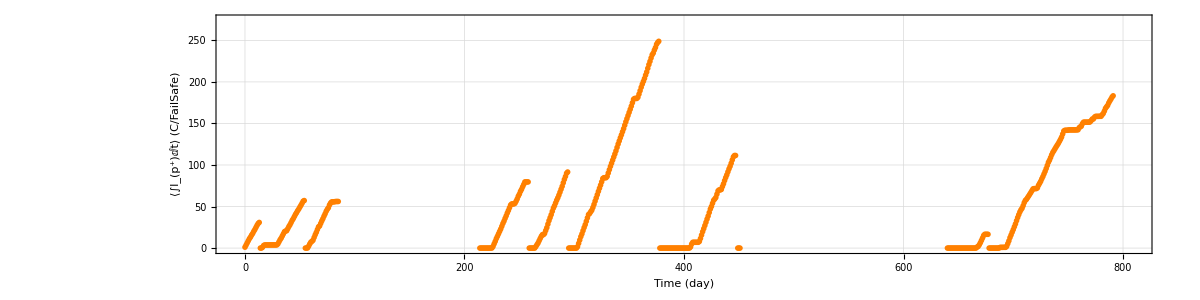

```mathematica
EDAListPlot[ptdata,PlotStyle->Blue,Frame->True,FrameLabel->{"Time (day)","# of UCN Kicks"},FrameTicks->{{LinTicks,None},{LinTicks,LinTicks}},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Bold,PlotRange->{{-10,810},{-10,299}},FrameStyle->{{Purple,Thickness[.004]},{Purple,Thickness[.004]},{Purple,Thickness[.004]},{Purple,Thickness[.004]}},PlotMarkers->{Automatic,Medium},AspectRatio->1/4,ImageSize->1200,GridLines->Automatic]
EDAListPlot[ptdata2,PlotStyle->Orange,Frame->{True,True,True,True},FrameLabel->{"Time (day)","⟨∫I_(p^+)ⅆt⟩ (C/day)"},FrameTicks->{{LinTicks,None},{LinTicks,LinTicks}},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Bold,FrameStyle->{{Red,Thickness[.004]},{Red,Thickness[.004]},{Red,Thickness[.004]},{Red,Thickness[.004]}},PlotMarkers->{Automatic,Medium},PlotRange->{{-10,810},{-.1,4.99}},AspectRatio->1/4,ImageSize->1200,GridLines->Automatic]
EDAListPlot[ptdata3,PlotStyle->Orange,Frame->{True,True,True,True},FrameLabel->{"Time (day)","⟨∫I_(p^+)ⅆt⟩ (C/FailSafe)"},FrameTicks->{{LinTicks,None},{LinTicks,LinTicks}},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Bold,FrameStyle->{{Red,Thickness[.004]},{Red,Thickness[.004]},{Red,Thickness[.004]},{Red,Thickness[.004]}},PlotMarkers->{Automatic,Medium},PlotRange->{{-10,810},{-1,275}},AspectRatio->1/4,ImageSize->1200,GridLines->Automatic]
```

## Detailed Plot

```mathematica
j=1;i=1;ptdatcorr={};ptdat2corr={};
diff={};ratio={};
tol=0.9;
While[((i<=Dimensions[ptdata][[1]])&&(j<=Dimensions[ptdata2][[1]])),
If[((Abs[ptdata[[i]][[1]]-ptdata2[[j]][[1]]]<tol)&&(ptdata2[[j]][[2]]≠0)&&(ptdata[[i]][[2]]≠0)),
ptdatcorr=AppendTo[ptdatcorr,ptdata[[i]]];
ptdat2corr=AppendTo[ptdat2corr,ptdata2[[j]]];
ratio=AppendTo[ratio,N[{ptdata[[i]][[1]],ptdata2[[j]][[2]]*1000/ptdata[[i]][[2]]}]];
];
diff=AppendTo[diff,N[Abs[ptdata[[i]][[1]]-ptdata2[[j]][[1]]]]];
If[((ptdata[[i]][[1]]-ptdata2[[j]][[1]])≥(tol)),
j++;,
If[((ptdata[[i]][[1]]-ptdata2[[j]][[1]])≤-(tol)),
i++;,
i++;j++;
];
];
];
(***)
```

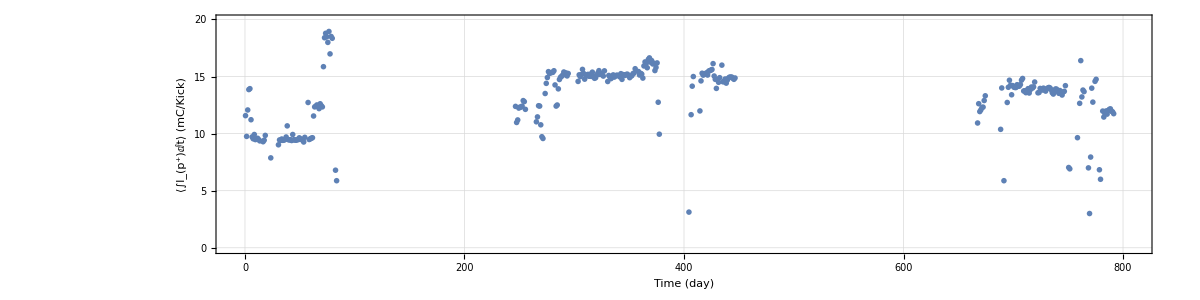

```mathematica
EDAListPlot[ratio,Frame->{True,True,True,True},FrameLabel->{{"⟨∫I_(p^+)ⅆt⟩ (mC/Kick)",""},{"Time (day)",""}},FrameTicks->{{LinTicks,None},{LinTicks,LinTicks}},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],PlotMarkers->{Automatic,Medium},PlotRange->{{-10,810},{-.1,19.99}},AspectRatio->1/4,ImageSize->1200,GridLines->Automatic]
```

## U+D calculations

```mathematica
sdata=ReadList[StringJoin[AscDir,seperator,"south_allmonths.txt"],metaStructure4];
ptsdata=Table[{0,0},{k,1,Dimensions[sdata][[1]]}];
k=1;ini=0;fin=0;
sttime=AbsoluteTime[DateObject[sdata[[1]][[1]]]];
send=Dimensions[sdata][[1]];
Parallelize[
For[i=2,i≤send,i++,
If[ToExpression[StringTake[sdata[[i]][[1]],{9,10}]]!=ToExpression[StringTake[sdata[[i-1]][[1]],{9,10}]],
ini=fin+1;
fin=i-1;
ptsdata[[k]]={(AbsoluteTime[StringJoin[StringTake[sdata[[ini]][[1]],{1,10}],"_12:00:00_UTC"]]-sttime)/(24*3600),Mean[sdata[[ini;;fin,2]]]+Mean[sdata[[ini;;fin,3]]]};
If[Abs[ptsdata[[k]][[2]]]>20000,
ptsdata[[k]][[2]]=0;
];
k++;
];
If[i==send,
ini=fin+1;
fin=send;
ptsdata[[k]]={(AbsoluteTime[StringJoin[StringTake[sdata[[ini]][[1]],{1,10}],"_12:00:00_UTC"]]-sttime)/(24*3600),Mean[sdata[[ini;;fin,2]]]+Mean[sdata[[ini;;fin,3]]]};
If[Abs[ptsdata[[k]][[2]]]>20000,
ptsdata[[k]][[2]]=0;
];
k++;
];
];
j=1;i=1;ptsdatcorr={};
sratio={};
tol=0.9;
While[((i<=Dimensions[ptsdata][[1]])&&(j<=Dimensions[ratio][[1]])),
If[((Abs[ptsdata[[i]][[1]]-ratio[[j]][[1]]]<tol)&&(ratio[[j]][[2]]≠0)&&(ptsdata[[i]][[2]]≠0)&&(ptsdata[[i]][[2]]/ratio[[j]][[2]]<1400)),
ptsdatcorr=AppendTo[ptsdatcorr,ptsdata[[i]]];
sratio=AppendTo[sratio,N[{ptsdata[[i]][[1]],ptsdata[[i]][[2]]/ratio[[j]][[2]]}]];
];
If[((ptsdata[[i]][[1]]-ratio[[j]][[1]])≥(tol)),
j++;,
If[((ptsdata[[i]][[1]]-ratio[[j]][[1]])≤-(tol)),
i++;,
i++;j++;
];
];
];
]//AbsoluteTiming
```

{775.332,Null}

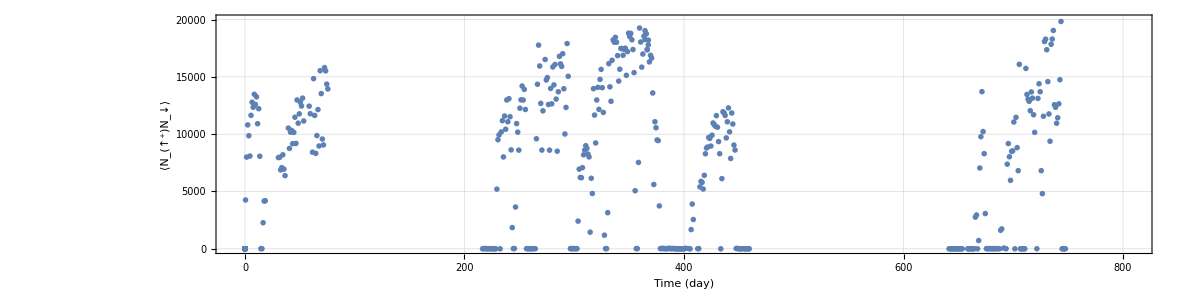

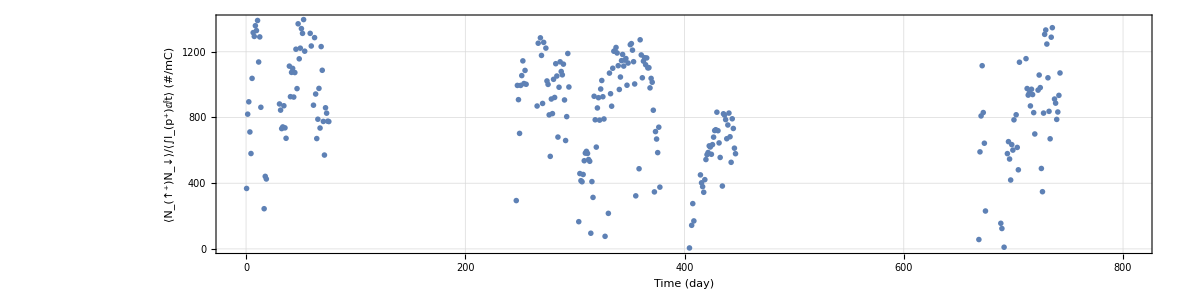

```mathematica
EDAListPlot[ptsdata,Frame->{True,True,True,True},FrameLabel->{{"⟨N_(↑^+)N_↓⟩",""},{"Time (day)",""}},FrameTicks->{{LinTicks,None},{LinTicks,LinTicks}},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],PlotMarkers->{Automatic,Medium},PlotRange->{{-10,810},{-10,19999}},AspectRatio->1/4,ImageSize->1200,GridLines->Automatic]
EDAListPlot[sratio,Frame->{True,True,True,True},FrameLabel->{{"⟨N_(↑^+)N_↓⟩/⟨∫I_(p^+)ⅆt⟩\n(#/mC)",""},{"Time (day)",""}},FrameTicks->{{LinTicks,None},{LinTicks,LinTicks}},TicksStyle->Directive[FontSize->40],LabelStyle->{34,Black},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],PlotMarkers->{Automatic,Medium},PlotRange->{{-11,810},Automatic},AspectRatio->1/4,ImageSize->1200,GridLines->Automatic]
```

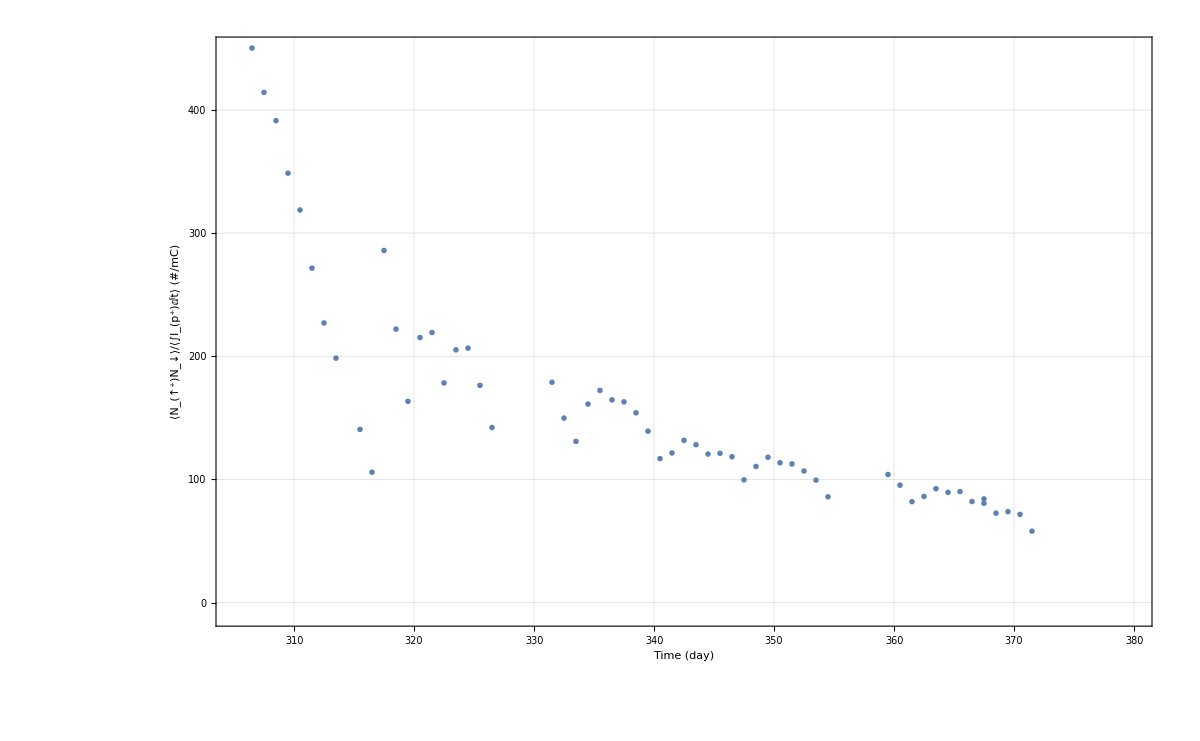

```mathematica
j=1;i=1;ptsdatcorr2={};
sratio2={};
tol=0.9;
While[((i<=Dimensions[ptsdata][[1]])&&(j<=Dimensions[ratio][[1]])),
If[((Abs[ptsdata[[i]][[1]]-ptdata3[[j]][[1]]]<tol)&&(ptdata3[[j]][[2]]≠0)&&(ptsdata[[i]][[2]]≠0)&&(ptsdata[[i]][[2]]/ptdata3[[j]][[2]]>50)),
ptsdatcorr2=AppendTo[ptsdatcorr2,ptsdata[[i]]];
sratio2=AppendTo[sratio2,N[{ptsdata[[i]][[1]],ptsdata[[i]][[2]]/ptdata3[[j]][[2]]}]];
];
If[((ptsdata[[i]][[1]]-ptdata3[[j]][[1]])≥(tol)),
j++;,
If[((ptsdata[[i]][[1]]-ptdata3[[j]][[1]])≤-(tol)),
i++;,
i++;j++;
];
];
];
EDAListPlot[sratio2,Frame->{True,True,True,True},FrameLabel->{{"⟨N_(↑^+)N_↓⟩/⟨∫I_(p^+)ⅆt⟩\n(#/mC)",""},{"Time (day)",""}},FrameTicks->{{LinTicks,None},{LinTicks,LinTicks}},TicksStyle->Directive[FontSize->40],LabelStyle->{34,Black},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],PlotMarkers->{Automatic,Medium},PlotRange->{{305,380},{-10,450}},ImageSize->1200,GridLines->Automatic]
```

```mathematica
sratio2
```

{{0.49834,3915.54},{1.49834,2217.41},{2.49834,1758.07},{3.49834,1133.67},{4.49834,721.375},{5.49834,885.625},{6.49834,820.558},{7.49834,702.707},{8.49834,669.015},{9.49834,564.066},{10.4983,533.106},{11.4983,398.259},{12.4983,413.617},{13.4983,261.543},{16.4983,2286.59},{17.4983,1317.24},{18.4983,1122.46},{30.4983,1561.96},{31.4983,1054.09},{32.4983,684.841},{33.4983,590.096},{34.4983,562.949},{35.4983,405.615},{36.4983,323.57},{39.4983,450.113},{40.4983,337.226},{41.4983,362.818},{42.4983,337.32},{43.4983,275.381},{44.4983,286.916},{45.4983,302.468},{46.4983,226.852},{47.4983,304.495},{48.4983,243.21},{49.4983,250.554},{50.4983,259.017},{51.4983,241.723},{52.4983,243.889},{53.4983,197.686},{58.4983,5380.87},{59.4983,2388.38},{61.4983,1039.25},{62.4983,1570.48},{63.4983,910.187},{64.4983,518.021},{65.4983,521.397},{68.4983,583.41},{69.4983,455.713},{70.4983,292.719},{71.4983,255.928},{72.4983,411.015},{73.4983,376.766},{74.4983,324.622},{75.4983,299.121},{224.498,98.7287},{225.498,20.2926},{229.498,456.654},{230.498,671.222},{231.498,579.785},{233.498,444.681},{234.498,426.245},{235.498,270.458},{236.498,357.031},{237.498,291.841},{238.498,334.479},{239.498,262.665},{240.498,289.595},{241.498,237.38},{242.498,166.586},{243.498,34.854},{244.498,0.244084},{245.498,0.447514},{246.498,67.6241},{247.498,194.03},{248.498,172.271},{249.498,137.927},{250.498,188.981},{251.498,190.524},{252.498,200.818},{253.498,175.762},{254.498,181.479},{255.498,152.644},{256.498,0.142068},{257.498,0.149282},{258.498,0.154191},{265.498,5146.96},{266.498,3571.31},{267.498,2956.32},{268.498,1807.37},{269.498,1098.58},{270.498,608.112},{271.498,744.165},{273.498,937.415},{274.498,696.975},{275.498,607.454},{276.498,436.753},{277.498,260.673},{278.498,382.139},{279.498,314.637},{280.498,358.806},{281.498,297.41},{282.498,315.763},{283.498,240.462},{284.498,147.707},{285.498,226.448},{286.498,263.475},{287.498,239.991},{288.498,224.782},{289.498,228.889},{290.498,177.765},{291.498,121.203},{292.498,143.174},{293.498,198.871},{294.498,164.395},{303.498,1416.76},{304.498,1233.54},{306.498,450.249},{307.498,414.242},{308.498,391.288},{309.498,348.662},{310.498,318.773},{311.498,271.511},{312.498,227.003},{313.498,198.448},{314.498,34.9063},{315.498,140.6},{316.498,105.813},{317.498,285.866},{318.498,222.048},{319.498,163.375},{320.498,215.163},{321.498,219.251},{322.498,178.288},{323.498,205.182},{324.498,206.576},{325.498,176.354},{326.498,142.105},{327.498,14.0262},{328.498,0.140233},{329.498,0.149554},{330.498,36.5463},{331.498,178.847},{332.498,149.757},{333.498,130.857},{334.498,161.133},{335.498,172.208},{336.498,164.539},{337.498,162.952},{338.498,154.062},{339.498,139.142},{340.498,116.854},{342.498,131.67},{344.498,120.554},{347.498,99.5799},{348.498,110.469},{350.498,113.468},{353.498,99.3962},{354.498,85.8375},{355.498,28.1384},{356.498,0.0715255},{357.498,0.0777139},{358.498,41.5129},{359.498,103.968},{360.498,95.2631},{361.498,81.9081},{362.498,86.1355},{363.498,92.4363},{364.498,89.4272},{365.498,90.1185},{366.498,82.0194},{367.498,84.1492},{367.498,80.6032},{368.498,72.5818},{369.498,73.7792},{370.498,71.5347},{371.498,57.9356},{372.498,23.5468},{373.498,45.9349},{374.498,43.0748},{375.498,38.3583},{376.498,37.9549},{404.498,725.},{406.498,1148.64},{407.498,779.621},{408.498,366.867},{412.498,1.05261},{413.498,1.82985},{414.498,676.607},{415.498,509.151},{416.498,369.816},{417.498,263.779},{418.498,273.458},{419.498,305.128},{421.498,254.382},{422.498,251.766},{423.498,225.046},{424.498,190.704},{425.498,197.833},{426.498,203.559},{427.498,188.435},{428.498,181.293},{429.498,190.862},{430.498,163.451},{431.498,135.911}}

## Other-Plot from W2-Ratio

```mathematica
ratiowhterror=Table[{ratio[[k]][[1]],ratio[[k]][[2]][[1]]},{k,1,Dimensions[ratio][[1]]}];
lineStyle0={Thick,Black};
lineStyle02={Thick,White};
lineStyle1={Thick,Orange,Dashed};
condidates={2,5,7.1,9,11,19,20,21.1,21.5,22.2,23.2,24.2,26.2,27,28.1,29.2,30.2,33.2,34,35,36,40,41,42,43,46,47.1,48.2,57,61,62,63.1,64.2,69,70,71,74,75,77,78,81,84,87,90};
line1=Table[Line[{{condidates[[k]],0},{condidates[[k]],.2}}],{k,1,Dimensions[condidates][[1]]}];
lineStyle2={Pink,Opacity[.15]};
rec1=Rectangle[{0,0},{27,1}];
lineStyle3={Green,Opacity[.15]};
rec2=Rectangle[{27,0},{90,1}];
lineStyle4={Gray,Opacity[.5]};
rec3=Rectangle[{27,0},{90,.054}];
rec4=Rectangle[{27,.096},{90,1}];
lineStyle5={Gray,Opacity[.75]};
rec5=Rectangle[{0,0},{27,.054}];
rec6=Rectangle[{0,.096},{27,1}];
show12=Show[{
Plot[{avgratio,avgratio+2sdratio,avgratio-2sdratio},{x,0,90},PlotStyle->{Automatic,{Black,Dashed},{Black,Dashed}},
Frame->True,PlotRange->{{0,90},{.04,.13}},FrameLabel->{"Time (days)","(U + D)/(West1× ϵ)"},TicksStyle->Directive[FontSize->40],FrameTicks->LinTicks,LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{3600},
Epilog->{
{Directive[lineStyle1],line1},
{Directive[lineStyle2],rec1},
{Directive[lineStyle3],rec2},
{Directive[lineStyle0],
Text[Style["t_(Beam - on - Target) ~ 5.4 s",FontSize->Large],{15,.12}],Text[Style["I_(Beam - on - Target) ~ 2.2 mA",FontSize->Large],{15,.115}],Text[Style["t_(Beam - on - Target) ~ 7.5 s",FontSize->Large],{31,.05}],Text[Style["I_(Beam - on - Target) ~ 2.0 mA",FontSize->Large],{26,.055}]
},
{Directive[lineStyle02],
Rotate[Text[Style["Fail-Safe",FontSize->52],{52,.08}],90 Degree]}
}
],
RegionPlot[(x>0 && x<22.2),{x,0,90},{y,.002,1},Mesh->100,MeshFunctions->{#1-300#2&},MeshShading->{{White,Opacity[.05]},{Gray,Opacity[.05]}},PlotStyle->None,BoundaryStyle->None],
RegionPlot[(x>22.2 && x<90),{x,0,90},{y,.002,1},Mesh->200,MeshFunctions->{#1+300#2&},MeshShading->{{White,Opacity[.05]},{Gray,Opacity[.05]}},PlotStyle->None,BoundaryStyle->None],
RegionPlot[(x>49 && x<55),{x,0,90},{y,0,1},PlotStyle->Black,BoundaryStyle->None],
EDAListPlot[ratio,
Frame->True,PlotRange->{{0,90},{.04,.13}},FrameLabel->{"Time (days)","(U  +  D)/(West1× ϵ)"},TicksStyle->Directive[FontSize->40],FrameTicks->LinTicks,LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{3600},PlotMarkers->{Automatic,None}
],
EDAListPlot[ratiowhterror,
Frame->True,PlotRange->{{0,90},{.04,.13}},PlotStyle->Red,FrameLabel->{"Time (days)","(U  +  D)/(West1× ϵ)"},TicksStyle->Directive[FontSize->40],FrameTicks->LinTicks,LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{3600},PlotMarkers->{Automatic,Small}
]
},AspectRatio->1/4]
```